```mathematica
(* set options for plots *)
SetOptions[{Plot,ListPlot,Histogram},PlotRange->All,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameStyle->Directive[Black],Frame->True,ImageSize->400];

(* set working directory *)
SetDirectory[NotebookDirectory[]];

(* default Mathematica colour scheme for plots *)
colors=ColorData[97,"ColorList"];

(* codes for colours, e.g. colors[[1]] etc *)
Grid[{Range[Length[colors]],colors}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
RGBColor[0.368417, 0.506779, 0.709798] | RGBColor[0.880722, 0.611041, 0.142051] | RGBColor[0.560181, 0.691569, 0.194885] | RGBColor[0.922526, 0.385626, 0.209179] | RGBColor[0.528488, 0.470624, 0.701351] | RGBColor[0.772079, 0.431554, 0.102387] | RGBColor[0.363898, 0.618501, 0.782349] | RGBColor[1, 0.75, 0] | RGBColor[0.647624, 0.37816, 0.614037] | RGBColor[0.571589, 0.586483, 0.] | RGBColor[0.915, 0.3325, 0.2125] | RGBColor[0.40082222609352647, 0.5220066643438841, 0.85] | RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142] | RGBColor[0.736782672705901, 0.358, 0.5030266573755369] | RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]

## Transcription model

### Model parameters

```mathematica
k12=0.001*60;
k21=0.0007*60;
k2=0.092*60;

(* RNA polymerase II elongation speed [kb/min]*)
(* source: In vivo dynamics of RNA polymerase II transcriptionhttps://doi.org/10.1038/nsmb1280Nonehttps://doi.org/10.1038/nsmb1280HyperlinkActionRecycledHyperlinkActive *)
vRNAP=2400.0;

(* median human gene length [kb] *)
(* source: NCBIhttps://www.ncbi.nlm.nih.gov/gene/18810Nonehttps://www.ncbi.nlm.nih.gov/gene/18810HyperlinkActionRecycledHyperlinkActive *)
geneL=10000.0;

(* measurement time [min] *)
T=SetPrecision[geneL/vRNAP,200*$MachinePrecision];

(* reinitiation to state K *)
K=2;

(* write everything in nice tables *)
rates=Grid[{{"k_12 [min^-1 ]","k_21 [min^-1 ]","k_2 [min^-1 ]"},{k12,k21,k2}},Frame->All,Background->{None,{LightGreen,None},None}]
Grid[{{"Elongation time [min]","State after reinitiation"},{N[T],K}},Frame->All,Background->{None,{LightBlue,None},None}]
```

k_12 [min^-1 ] | k_21 [min^-1 ] | k_2 [min^-1 ]
0.06 | 0.042 | 5.52

Elongation time [min] | State after reinitiation
4.16667 | 2

### Distribution of the waiting time between two nascent RNA production events

```mathematica
(* set precision of all the rates *)
dummy=SetPrecision[k12,200*$MachinePrecision];
k12=dummy;
dummy=SetPrecision[k21,200*$MachinePrecision];
k21=dummy;
dummy=SetPrecision[k2,200*$MachinePrecision];
k2=dummy;

(* Laplace transform of the waiting time distribution *)
SuperStar[f][s_]:=(k2*(s+k12))/(s^2+(k12+k21+k2)*s+k2*k12);

(* find the mean initiation time [s]*)
μ=-D[SuperStar[f][s],{s,1}]/.s->0;

(* find the standard deviation of the waiting time [s] *)
σ=√((D[SuperStar[f][s],{s,2}]/.s->0)-μ*μ);

(* find the Fano factor *)
FFwt=σ^2/μ;

(* write everything in a nice table *)
Grid[{{"Mean initiation time [min]","Standard deviation [min]","Fano factor"},{N[μ],N[σ],N[FFwt]}},Frame->All,Background->{None,{LightOrange,None},None}]
```

Mean initiation time [min] | Standard deviation [min] | Fano factor
0.307971 | 2.07892 | 14.0335

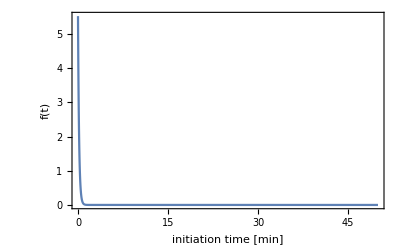

```mathematica
(* plot the waiting time distribution *)
f[t_]:=InverseLaplaceTransform[SuperStar[f][s],s,t]
plot1=Plot[f[SetPrecision[t,100*$MachinePrecision]],{t,0,50},FrameLabel->{"initiation time [min]","f(t)"}]
```

```mathematica
(* export waiting time distribution to a file *)
dataf=Table[{0.01*t,N[f[SetPrecision[0.01*t,100*$MachinePrecision]]]},{t,1,200}];
```

```mathematica
Export["wt-dist-model-1-exact.csv",dataf]
```

wt-dist-model-1-exact.csv

### Nascent RNA distribution (stationary state)

```mathematica
(* h[s]=1-f^*[s] *)
SuperStar[h][s_]:=(s^2+(k12+k21)*s)/(s^2+(k12+k21+k2)*s+k2*k12);

(* find mean of the nascent RNA *)
Subscript[μ, N]=T/μ; 

(* find variance of the nascent RNA *)
VarN=Re[InverseLaplaceTransform[(1+SuperStar[f][s])/(μ*s^2*SuperStar[h][s]),s,T]-Subscript[μ, N]*Subscript[μ, N]];

(* find standard deviation of the nascent RNA*)
Subscript[σ, N]=√VarN;

(* find the Fano factor*)
FFN=VarN/Subscript[μ, N];

(* write everything in a nice table *)
Grid[{{"mean nascent RNA","standard deviation","Fano factor"},{N[Subscript[μ, N]],N[Subscript[σ, N]],N[FFN]}},Frame->All,Background->{None,{LightMagenta,None},None}]
```

mean nascent RNA | standard deviation | Fano factor
13.5294 | 11.1931 | 9.26017

```mathematica
(* Laplace transform of the nascent RNA distribution *)
SuperStar[P][n_,s_]:=If[n==0,1/s-(SuperStar[h][s])/(μ*s^2),1/μ*((SuperStar[h][s])/s)^2*(SuperStar[f][s])^(n-1)]

(* nascent RNA distribution *)
P=Table[{n,N[InverseLaplaceTransform[SuperStar[P][n,s],s,T]]},{n,0,44}]

(* check the normalisation *)
Total[P[[All,2]]]
```

{{0,0.328313},{1,0.00767838},{2,0.00772545},{3,0.00777161},{4,0.00781715},{5,0.00786328},{6,0.00791381},{7,0.007979},{8,0.00808238},{9,0.00827097},{10,0.00862671},{11,0.00927458},{12,0.0103799},{13,0.012128},{14,0.0146829},{15,0.0181317},{16,0.0224279},{17,0.027354},{18,0.0325221},{19,0.0374189},{20,0.04149},{21,0.044242},{22,0.0453362},{23,0.0446482},{24,0.0422818},{25,0.0385344},{26,0.0338306},{27,0.0286407},{28,0.023406},{29,0.0184839},{30,0.0141196},{31,0.0104433},{32,0.00748603},{33,0.00520537},{34,0.00351409},{35,0.00230509},{36,0.00147034},{37,0.000912688},{38,0.000551707},{39,0.000324989},{40,0.000186672},{41,0.000104619},{42,0.0000572411},{43,0.0000305929},{44,0.00001598}}

0.999984

```mathematica
(* plot the nascent RNA distribution *)
plot2=ListPlot[P,PlotMarkers->Automatic,FrameLabel->{"nascent RNA number n","P(N=n)"}]
```

```mathematica
(* export the nascent RNA distribution to a file *)
Export["nascent-RNA-dist-model-1-exact.csv",P]
```

nascent-RNA-dist-model-1-exact.csv